```mathematica
(* Solving the Euler angles *)
```

```mathematica
n=3;ep=LeviCivitaTensor[3,List];alcoord={al,be,ga};alcoordd={aldot,bedot,gadot};phcoord={phx,phy,phz};phcoordd={phxdot,phydot,phzdot};phpcoord={phpx,phpy,phpz};phpcoordd={phpxdot,phpydot,phpzdot};gap={gapx,gapy,gapz};reuler={{Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga],Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga],Sin[be] Sin[ga]},{-Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga],Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga],Cos[ga] Sin[be]},{Sin[al] Sin[be],-Cos[al] Sin[be],Cos[be]}};inversereuler=Simplify[Inverse[reuler]];MatrixForm[inversereuler]
```

(Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga] | -Cos[be] Cos[ga] Sin[al]-Cos[al] Sin[ga] | Sin[al] Sin[be]
Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga] | Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga] | -Cos[al] Sin[be]
Sin[be] Sin[ga] | Cos[ga] Sin[be] | Cos[be])

```mathematica
(* angular velocity *)
```

```mathematica
tranalphp={{Sin[be]*Sin[ga],Cos[ga],0},{Sin[be]*Cos[ga],-Sin[ga],0},{Cos[be],0,1}};inversetranalphp=Simplify[Inverse[tranalphp]];omp=tranalphp.alcoordd;omi=Simplify[inversereuler.omp,Assumptions->{al∈Reals,be∈Reals,ga∈Reals}];ompf=omp/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};omif=omi/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};xpaxis={Cos[al]*Cos[ga]-Sin[al]*Cos[be]*Sin[ga],Sin[al]*Cos[ga]+Cos[al]*Cos[be]*Sin[ga],Sin[be]*Sin[ga]};ypaxis={-Cos[al]*Sin[ga]-Sin[al]*Cos[be]*Cos[ga],-Sin[al]*Sin[ga]+Cos[al]*Cos[be]*Cos[ga],Sin[be]*Cos[ga]};zpaxis={Sin[be]*Sin[al],-Sin[be]*Cos[al],Cos[be]};xpaxisf=xpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};ypaxisf=ypaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};zpaxisf=zpaxis/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]};
```

```mathematica
(* kinetic energy *)
```

```mathematica
ip={{ipxx,0,0},{0,ipyy,0},{0,0,ipzz}};tp=Simplify[1/2*Sum[ip[[i,j]]*omp[[i]]*omp[[j]],{i,1,n},{j,1,n}]];lp=ip.omp;li=Simplify[inversereuler.lp,Assumptions->{al∈Reals,be∈Reals,ga∈Reals}];MatrixForm[li]
```

(ipzz (gadot+aldot Cos[be]) Sin[al] Sin[be]-ipyy (aldot Cos[ga] Sin[be]-bedot Sin[ga]) (Cos[be] Cos[ga] Sin[al]+Cos[al] Sin[ga])+ipxx (Cos[al] Cos[ga]-Cos[be] Sin[al] Sin[ga]) (bedot Cos[ga]+aldot Sin[be] Sin[ga])
-ipzz Cos[al] (gadot+aldot Cos[be]) Sin[be]+ipyy (aldot Cos[ga] Sin[be]-bedot Sin[ga]) (Cos[al] Cos[be] Cos[ga]-Sin[al] Sin[ga])+ipxx (Cos[ga] Sin[al]+Cos[al] Cos[be] Sin[ga]) (bedot Cos[ga]+aldot Sin[be] Sin[ga])
gadot ipzz Cos[be]+aldot ipzz Cos[be]^2+Sin[be] (aldot ipyy Cos[ga]^2 Sin[be]+bedot (ipxx-ipyy) Cos[ga] Sin[ga]+aldot ipxx Sin[be] Sin[ga]^2))

```mathematica
(* potential energy *)
```

```mathematica
scoeffi={{sxx,sxy,sxz},{sxy,syy,syz},{sxz,syz,szz}};scoeffp=Table[Simplify[Sum[reuler[[k,i]]*reuler[[l,j]]*scoeffi[[i,j]],{i,1,n},{j,1,n}]],{k,1,n},{l,1,n}];deeg=cc*scoeffp[[3,3]];
```

```mathematica
(* Euler equation *)
```

```mathematica
gaplv=Table[Simplify[Sum[-2*cc*scoeffi[[j,k]]*reuler[[3,k]]*inversereuler[[j,l]]*ep[[i,3,l]],{j,1,n},{k,1,n},{l,1,n}]],{i,1,n}];eueq1=Table[Simplify[D[Sum[ip[[i,j]]*ompf[[j]],{j,1,n}],t]+Sum[ip[[j,k]]*omp[[j]]*omp[[l]]*ep[[l,k,i]],{j,1,n},{k,1,n},{l,1,n}]-gaplv[[i]]/.{al->alf[t],be->bef[t],ga->gaf[t]}],{i,1,n}]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga};eueq2=Table[Simplify[Sum[eueq1[[i]]*tranalphp[[i,j]],{i,1,n}]],{j,1,n}];gaallv=Table[Simplify[-D[deeg,alcoord[[i]]]],{i,1,n}];eueq4=Table[Simplify[D[D[tp,alcoordd[[i]]]/.{al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t]},t]-D[tp,alcoord[[i]]]-gaallv[[i]]/.{alf''[t]->alddot,bef''[t]->beddot,gaf''[t]->gaddot,alf'[t]->aldot,bef'[t]->bedot,gaf'[t]->gadot,alf[t]->al,bef[t]->be,gaf[t]->ga}],{i,1,n}];
```

```mathematica
(* numerical values *)
```

```mathematica
cc1=1;sxx1=0.02;syy1=0.01;szz1=-0.04;sxy1=0.0;sxz1=0.0;syz1=0;ipxx1=1;ipyy1=1;ipzz1=1.1;tf1=800;numeueq=eueq4/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1,ipxx->ipxx1,ipyy->ipyy1,ipzz->ipzz1,al->alf[t],be->bef[t],ga->gaf[t],aldot->alf'[t],bedot->bef'[t],gadot->gaf'[t],alddot->alf''[t],beddot->bef''[t],gaddot->gaf''[t]};deeg1=deeg/.{cc->cc1,sxx->sxx1,syy->syy1,szz->szz1,sxy->sxy1,sxz->sxz1,syz->syz1};
```

```mathematica
(* 1. stationary spinning *)
```

```mathematica
(* initial values *)
```

```mathematica
al01=Pi/2;be01=1.2;peramp1=0.01;vp1=Pi/2;omz1=1;om1=omz1*ipzz1/ipxx1;perpre1=(cc1*(2*szz1-sxx1-syy1)*Cos[be01])/(ipzz1*omz1);al1=al01-peramp1/(om1*Sin[be01])*Cos[vp1]+Cos[be01]*(sxx1-syy1)/(2*(2*szz1-sxx1-syy1)*Cos[be01])*Sin[2*al01];be1=be01+peramp1/om1*Sin[vp1]-Sin[be01]*(sxx1-syy1)/(2*(2*szz1-sxx1-syy1)*Cos[be01])*Cos[2*al01];aldot1=perpre1+peramp1/Sin[be01]*Sin[vp1]+Cos[be01]*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Cos[2*al01];bedot1=peramp1*Cos[vp1]+Sin[be01]*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*al01];ga1=0;gadot1=omz1-aldot1*Cos[be1];peralf1=al01+perpre1*t-peramp1/(Sin[be01]*om1)*Cos[om1*t+vp1]+Cos[be01]*(cc1*(sxx1-syy1))/(ipzz1*omz1)*1/(2*perpre1)*Sin[2*perpre1*t+2*al01];perbef1=be01+peramp1/om1*Sin[om1*t+vp1]-Sin[be01]*(cc1*(sxx1-syy1))/(ipzz1*omz1)*1/(2*perpre1)*Cos[2*perpre1*t+2*al01];pergaf1=omz1*t-(peralf1-al1)*Cos[be01];Print[{al1,be1,ga1},"\n",{aldot1,bedot1,gadot1}]
```

{1.5708,1.09217,0}
{-0.0288008,0.,1.01326}

```mathematica
solal=NDSolve[{numeueq[[1]]==0,numeueq[[2]]==0,numeueq[[3]]==0,alf[0]==al1,bef[0]==be1,gaf[0]==ga1,alf'[0]==aldot1,bef'[0]==bedot1,gaf'[0]==gadot1},{alf,bef,gaf},{t,0,tf1}]
```

{{alf→InterpolatingFunction[{{0., 800.}}, <>],bef→InterpolatingFunction[{{0., 800.}}, <>],gaf→InterpolatingFunction[{{0., 800.}}, <>]}}

```mathematica
t2=200;Show[{ParametricPlot3D[{{xpaxisf[[1]]/.solal[[1]],xpaxisf[[2]]/.solal[[1]],xpaxisf[[3]]/.solal[[1]]},{zpaxisf[[1]]/.solal[[1]],zpaxisf[[2]]/.solal[[1]],zpaxisf[[3]]/.solal[[1]]}},{t,0,t2},AxesLabel->{x,y,z}],Graphics3D[{Orange,Arrow[{{0,0,0},zpaxisf/.{t->0}/.solal[[1]]}]}],Graphics3D[{Orange,Dashed,Arrow[{{0,0,0},zpaxisf/.{t->t2}/.solal[[1]]}]}],Graphics3D[{Blue,Arrow[{{0,0,0},xpaxisf/.{t->0}/.solal[[1]]}]}],Graphics3D[{Blue,Dashed,Arrow[{{0,0,0},xpaxisf/.{t->t2}/.solal[[1]]}]}]}]
```

-Graphics3D-

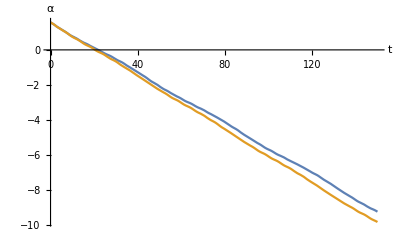

```mathematica
Plot[{Evaluate[alf[t]/.solal[[1]]],peralf1},{t,0,150},AxesLabel->{"t","α"},PlotRange->All]
```

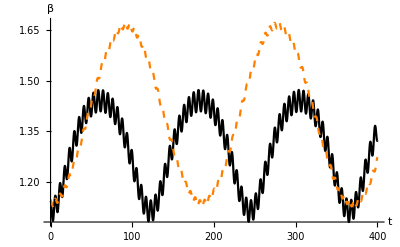

```mathematica
Plot[{Evaluate[bef[t]/.solal[[1]]],perbef1},{t,0,400},AxesLabel->{"t","β"},PlotRange->All,PlotStyle->{Black,{Dashed,Orange}}]
```

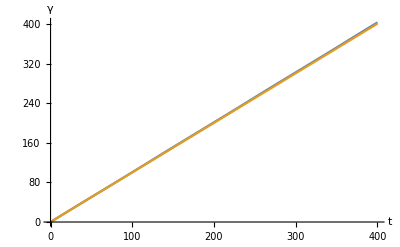

```mathematica
Plot[{Evaluate[gaf[t]/.solal[[1]]],pergaf1},{t,0,400},AxesLabel->{"t","γ"},PlotRange->All]
```

```mathematica
(* write data file *)
```

```mathematica
SetDirectory["~/Yandex.Disk/Documents/research/kiaa/lvprecession/anime"];
```

```mathematica
Npt=1000;tf2=200;dt=tf2/(Npt-1);data=Table[{N[(i-1)*dt],N[alf[(i-1)*dt]/.solal[[1]]],N[bef[(i-1)*dt]/.solal[[1]]],N[gaf[(i-1)*dt]/.solal[[1]]],N[xpaxisf[[1]]/.{t->(i-1)*dt}/.solal[[1]]],N[xpaxisf[[2]]/.{t->(i-1)*dt}/.solal[[1]]],N[xpaxisf[[3]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[1]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[2]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[3]]/.{t->(i-1)*dt}/.solal[[1]]]},{i,1,Npt}];Export["sp1.dat",data]
```

```mathematica
(* 2. free precession *)
```

```mathematica
(* initial values *)
```

```mathematica
al01=N[Pi/2];be01=0.7;peramp1=0.4;vp1=N[Pi/2];omz1=1;om1=omz1*ipzz1/ipxx1;perpre1=om1/Cos[be01]-(cc1*(2*szz1-sxx1-syy1)*Cos[be01])/(ipzz1*omz1);al1=al01+peramp1/(om1*Sin[be01])*Cos[vp1]+(Cos[be01]*((Cos[be01])^2+2))/(4-(Cos[be01])^2)*1/(2*perpre1)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*al01];be1=be01+peramp1/om1*Sin[vp1]-(3*Sin[be01]*(Cos[be01])^2)/(4-(Cos[be01])^2)*1/(2*perpre1)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Cos[2*al01];aldot1=perpre1-peramp1/Sin[be01]*Sin[vp1]+(Cos[be01]*((Cos[be01])^2+2))/(4-(Cos[be01])^2)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Cos[2*al01];bedot1=peramp1*Cos[vp1]+(3*Sin[be01]*(Cos[be01])^2)/(4-(Cos[be01])^2)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*al01];ga1=0;gadot1=omz1-aldot1*Cos[be1];peralf1=al01+perpre1*t+peramp1/(om1*Sin[be01])*Cos[om1*t+vp1]+(Cos[be01]*((Cos[be01])^2+2))/(4-(Cos[be01])^2)*1/(2*perpre1)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*perpre1*t+2*al01];perbef1=be01+peramp1/om1*Sin[om1*t+vp1]-(3*Sin[be01]*(Cos[be01])^2)/(4-(Cos[be01])^2)*1/(2*perpre1)*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Cos[2*perpre1*t+2*al01];pergaf1=omz1*t-(peralf1-al1)*Cos[be01]+perpre1*Sin[be01]*((-peramp1/om1^2*Cos[om1*t+vp1]-(3*Sin[be01]*(Cos[be01])^2)/(4-(Cos[be01])^2)*1/(2*perpre1)^2*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*perpre1*t+2*al01])-(-peramp1/om1^2*Cos[vp1]-(3*Sin[be01]*(Cos[be01])^2)/(4-(Cos[be01])^2)*1/(2*perpre1)^2*(cc1*(sxx1-syy1))/(ipzz1*omz1)*Sin[2*al01]));Print[{al1,be1,ga1},"\n",{aldot1,bedot1,gadot1}]
```

{1.5708,1.06463,0}
{0.888518,2.48615×10^-17,0.569222}

```mathematica
solal=NDSolve[{numeueq[[1]]==0,numeueq[[2]]==0,numeueq[[3]]==0,alf[0]==al1,bef[0]==be1,gaf[0]==ga1,alf'[0]==aldot1,bef'[0]==bedot1,gaf'[0]==gadot1},{alf,bef,gaf},{t,0,tf1}]
```

{{alf→InterpolatingFunction[{{0., 800.}}, <>],bef→InterpolatingFunction[{{0., 800.}}, <>],gaf→InterpolatingFunction[{{0., 800.}}, <>]}}

```mathematica
t2=100;Show[{ParametricPlot3D[{{xpaxisf[[1]]/.solal[[1]],xpaxisf[[2]]/.solal[[1]],xpaxisf[[3]]/.solal[[1]]},{zpaxisf[[1]]/.solal[[1]],zpaxisf[[2]]/.solal[[1]],zpaxisf[[3]]/.solal[[1]]}},{t,0,t2},AxesLabel->{x,y,z}],Graphics3D[{Orange,Arrow[{{0,0,0},zpaxisf/.{t->0}/.solal[[1]]}]}],Graphics3D[{Orange,Dashed,Arrow[{{0,0,0},zpaxisf/.{t->t2}/.solal[[1]]}]}],Graphics3D[{Blue,Arrow[{{0,0,0},xpaxisf/.{t->0}/.solal[[1]]}]}],Graphics3D[{Blue,Dashed,Arrow[{{0,0,0},xpaxisf/.{t->t2}/.solal[[1]]}]}]}]
```

-Graphics3D-

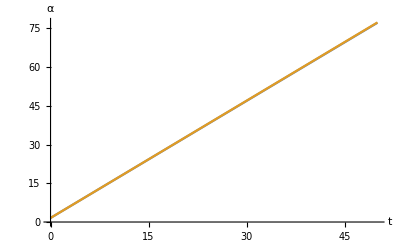

```mathematica
Plot[{Evaluate[alf[t]/.solal[[1]]],peralf1},{t,0,50},AxesLabel->{"t","α"}]
```

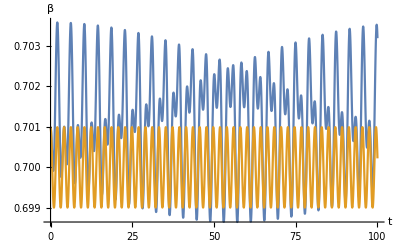

```mathematica
Plot[{Evaluate[bef[t]/.solal[[1]]],perbef1},{t,0,100},AxesLabel->{"t","β"},PlotRange->All]
```

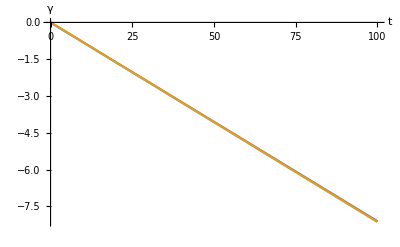

```mathematica
Plot[{Evaluate[gaf[t]/.solal[[1]]],pergaf1},{t,0,100},AxesLabel->{"t","γ"},PlotRange->All]
```

```mathematica
(* write data file *)
```

```mathematica
SetDirectory["~/Yandex.Disk/Documents/research/kiaa/lvprecession/anime"];
```

```mathematica
Npt=1000;tf2=200;dt=tf2/(Npt-1);data=Table[{N[(i-1)*dt],N[alf[(i-1)*dt]/.solal[[1]]],N[bef[(i-1)*dt]/.solal[[1]]],N[gaf[(i-1)*dt]/.solal[[1]]],N[xpaxisf[[1]]/.{t->(i-1)*dt}/.solal[[1]]],N[xpaxisf[[2]]/.{t->(i-1)*dt}/.solal[[1]]],N[xpaxisf[[3]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[1]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[2]]/.{t->(i-1)*dt}/.solal[[1]]],N[zpaxisf[[3]]/.{t->(i-1)*dt}/.solal[[1]]]},{i,1,Npt}];Export["tp1.dat",data]
```